# My glucose series

## Program

```mathematica
getTimeSer[gs_]:=Module[{tr},
tr=Transpose[gs];
TimeSeries[tr[[2]],{tr[[1]]}]]
```

```mathematica
getMarkPos[ser_]:=Position[ser,"*"]
```

```mathematica
getMarkedDate[ser_]:=Module[{pos},
pos=Map[#[[1]]&,Position[ser,"*"]];
Map[#[[1]]&,ser[[pos]]]
]
```

```mathematica
timeShift=2209021200
```

2209021200

```mathematica
createEpilog[gs_]:=Map[Text["*",{UnixTime[#]+timeShift,80}]&,getMarkedDate[gs]]
```

## Data

```mathematica
gs=Get["/Users/kouamano/Profile/blood-glc.txt"]
```

{{Thu 3 Feb 2022 06:05:00GMT+9,148,{}},{Thu 3 Feb 2022 11:16:00GMT+9,396,{}},{Thu 3 Feb 2022 16:31:00GMT+9,257,{}},{Fri 4 Feb 2022 06:06:00GMT+9,177,{}},{Fri 4 Feb 2022 11:16:00GMT+9,273,{}},{Fri 4 Feb 2022 18:30:00GMT+9,204,{}},{Sat 5 Feb 2022 05:57:00GMT+9,98,{}},{Sat 5 Feb 2022 12:15:00GMT+9,137,{}},{Sat 5 Feb 2022 17:15:00GMT+9,226,{}},{Sun 6 Feb 2022 06:08:00GMT+9,181,{*}},{Sun 6 Feb 2022 12:21:00GMT+9,374,{}},{Sun 6 Feb 2022 17:28:00GMT+9,241,{}},{Mon 7 Feb 2022 06:17:00GMT+9,158,{}},{Mon 7 Feb 2022 11:34:00GMT+9,293,{}},{Mon 7 Feb 2022 16:44:00GMT+9,382,{}},{Tue 8 Feb 2022 06:23:00GMT+9,152,{}},{Tue 8 Feb 2022 12:09:00GMT+9,399,{}},{Tue 8 Feb 2022 17:05:00GMT+9,275,{}},{Wed 9 Feb 2022 05:52:00GMT+9,116,{*}},{Wed 9 Feb 2022 11:54:00GMT+9,348,{}},{Wed 9 Feb 2022 17:04:00GMT+9,271,{}},{Thu 10 Feb 2022 06:21:00GMT+9,216,{}},{Thu 10 Feb 2022 11:54:00GMT+9,133,{}},{Thu 10 Feb 2022 17:01:00GMT+9,264,{}},{Fri 11 Feb 2022 06:25:00GMT+9,191,{}},{Fri 11 Feb 2022 12:00:00GMT+9,197,{}},{Fri 11 Feb 2022 17:04:00GMT+9,224,{}},{Sat 12 Feb 2022 06:23:00GMT+9,165,{}},{Sat 12 Feb 2022 12:09:00GMT+9,210,{}},{Sat 12 Feb 2022 17:09:00GMT+9,213,{}}}

Basic items

```mathematica
startTime=UnixTime[gs[[1,1]]]+timeShift;
endTime=UnixTime[gs[[-1,1]]]+timeShift;
```

```mathematica
gts=getTimeSer[gs]
```

TimeSeries[…]

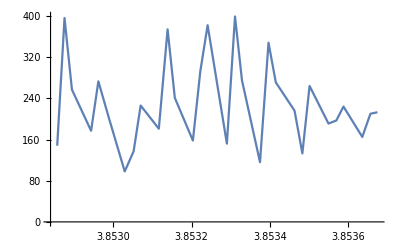

```mathematica
ListLinePlot[gts]
```

```mathematica
createEpilog[gs]
```

{Text[*,{3853116480,80}],Text[*,{3853374720,80}]}

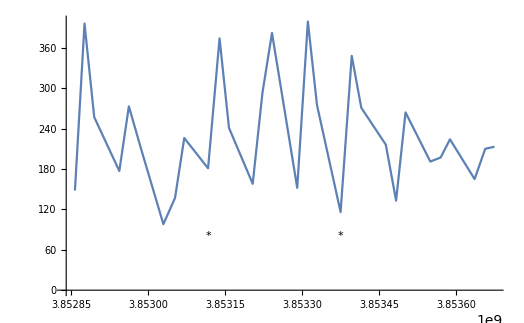

```mathematica
ListLinePlot[gts,Epilog->createEpilog[gs]]
```

Shift

```mathematica
1643835900-3852857100
```

-2209021200

```mathematica
Interpolation[gts]
```

InterpolatingFunction[…]

```mathematica
InterpolatingFunction[…][3852857100]
```

148

```mathematica
Range[startTime,endTime,1000]//Length
```

818

```mathematica
InterpolatingFunction[…][Range[startTime,endTime,1000]]//N;
```

```mathematica
Fourier[InterpolatingFunction[…][Range[startTime,endTime,1000]]//N]//Abs;
```

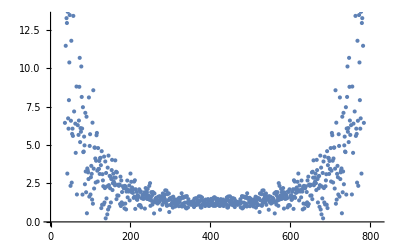

```mathematica
ListPlot[Fourier[InterpolatingFunction[…][Range[startTime,endTime,1000]]//N]//Abs]
```